## Setup

This setup uses (n,η) variables instead of (ρ,η).

### PDE solver

```mathematica
ClearAll@runTwoComponentSim;
Options[runTwoComponentSim]=Join[Options[NDSolve],{"GridPoints"->200,"BC"->"Reflective"}];
runTwoComponentSim[{fhat_,uSource_,vSource_},params_,{nInit_,etaInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[n[x,t],t]==Dv D[eta[x,t],{x,2}]
+(eps (uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),D[eta[x,t],t]==Dv (1+Du/Dv) D[eta[x,t],{x,2}]-Du D[n[x,t],{x,2}]
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->n[x,t],η->eta[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
n[0,t]==n[L,t],eta[0,t]==eta[L,t],(D[n[x,t],x]/.x->0)==(D[n[x,t],x]/.x->L),(D[eta[x,t],x]/.x->0)==(D[eta[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[n[x,t],x]/.x->0)==0,(D[eta[x,t],x]/.x->0)==0,(D[n[x,t],x]/.x->L)==0,(D[eta[x,t],x]/.x->L)==0
}
],
(* initial condition *)
n[x,0]==nInit[x],
eta[x,0]==etaInit[x]
}/.params,
{n,eta},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Curvature-dependent grid construction

Gets an continuous (e.g. interpolated) function on [0,1]. The phi parameter sets the approximate angle between the linear interpolations in two neighboring segments of the discretization. filterWidth sets the smoothing width for the grid.

```mathematica
ClearAll@uGConstr;
Options[uGConstr]={"dxMax"->1/150,"phi"->Pi/180*10,"filterWidth"->20, "ptsMax"->1000};
uGConstr[approxSol_,OptionsPattern[]]:=First@Last@Reap[Block[{
discApproxSol=D[approxSol[x],{x,2}]/.Partition[Thread[x->(Range[1/(2*OptionValue["ptsMax"]),1,1/OptionValue["ptsMax"]])],1],
smoothedGridDensityMeasure,
dxMin,
dx,
dxC=0,
dxNew=0,
xC=0,
xNew=0,
fdx,
i=0,
iMax=OptionValue["ptsMax"]
},
smoothedGridDensityMeasure=Interpolation[Transpose@{Range[1/(2*OptionValue["ptsMax"]),1,1/OptionValue["ptsMax"]],GaussianFilter[MaxFilter[Abs@discApproxSol,OptionValue["filterWidth"]],OptionValue["filterWidth"]]}];
fdx=1/(1/OptionValue["dxMax"]+smoothedGridDensityMeasure[x]/OptionValue["phi"]);
dxMin=1/(1/OptionValue["dxMax"]+Max[GaussianFilter[MaxFilter[Abs@discApproxSol,OptionValue["filterWidth"]],OptionValue["filterWidth"]]]/OptionValue["phi"]);
dxC=dx/.FindRoot[dx==fdx/.x->(dx/2),{dx,(dxMin+OptionValue["dxMax"])}];
xC=dxC/2;
Sow@xC;
While[xC<(1-dxMin/2),
i=i+1;
If[i>iMax,Print["Maximal number of grid points reached. Could not finish grid due to too sharp kinks."];Break[]];
dxNew=fdx/.x->Min[{(xC+dxC),1-1/(2*OptionValue["ptsMax"])}];
xNew=xC+(dxC+dxNew)/2;
If[xNew>(1-dxMin/2),Break[]];
Sow@xNew;
dxC=dxNew;
xC=xNew;
]
]
];
```

Laplace matrix on nonuniform grid. It has to be multiplied by 1/L^2 to represent the Laplacian in the natural units.

```mathematica
ClearAll@laplaceMatrixAS;
ClearAll@laplaceMatrixS;
```

```mathematica
laplaceMatrixAS[UnitGrid_?VectorQ]:=With[{vars=Table[u[i],{i,1,Length@UnitGrid}]},D[NDSolve`FiniteDifferenceDerivative[Derivative[2],Join[{-UnitGrid[[1]]},UnitGrid,{2-UnitGrid[[-1]]}],DifferenceOrder->1][Join[{vars[[1]]},vars,{-vars[[-1]]}]],{vars}]][[2;;-2]];
```

```mathematica
laplaceMatrixS[UnitGrid_?VectorQ]:=With[{vars=Table[u[i],{i,1,Length@UnitGrid}]},D[NDSolve`FiniteDifferenceDerivative[Derivative[2],Join[{-UnitGrid[[1]]},UnitGrid,{2-UnitGrid[[-1]]}],DifferenceOrder->1][Join[{vars[[1]]},vars,{vars[[-1]]}]],{vars}]][[2;;-2]];
```

They are overloaded to the laplaceMatrixAS/laplaceMatrixS for the uniform grid.

```mathematica
laplaceMatrixAS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-3,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

```mathematica
laplaceMatrixS[n_?NumericQ]:=SparseArray[{
{1,1}->-1,{-1,-1}->-1,
{i_,i_}->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{n,n}
]*n^2;
```

### Finite difference equations for stationary state

```mathematica
ClearAll@discreteLaplace;
discreteLaplace[data_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2]*Length[data]^2
];
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
Options@setupFiniteDifferenceEqs=Options@uGConstr;
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},gridRes_?NumericQ]:=With[{
nVec=Thread[n@Range[gridRes]],
etaVec=Thread[eta@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->{
Dv discreteLaplace[etaVec]/L^2
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
(Du+Dv) discreteLaplace[etaVec]/L^2
-Du discreteLaplace[nVec]/L^2
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
]
```

Overloading for the nonuniform grid. profileFn is the interpolated profile to which the grid will be build.

```mathematica
setupFiniteDifferenceEqs[{fhat_,uSource_,vSource_},profileFn_?((Head[#]==Function||Head[#]==InterpolatingFunction)&),opts:OptionsPattern[]]:=Block[{
UnitGrid=uGConstr[profileFn,Sequence@opts],
nVec,
etaVec
},
nVec=Thread[n@Range[Length@UnitGrid]];
etaVec=Thread[eta@Range[Length@UnitGrid]];
<|
"UnitGrid"->UnitGrid,
"nVec"->nVec,
"etaVec"->etaVec,
"Vars"->Join[nVec,etaVec],
"Weights"->SetPrecision[Differences[Join[{0},MovingAverage[UnitGrid,2],{1}]],110],
"Eqs"->{
Dv(SetPrecision[laplaceMatrixS[UnitGrid],110].etaVec)/L^2
+(eps(uSource+vSource)/.{n->nVec,η->etaVec}),
(Du+Dv)(SetPrecision[laplaceMatrixS[UnitGrid],110].etaVec)/L^2
-Du(SetPrecision[laplaceMatrixS[UnitGrid],110].nVec)/L^2
+(-fhat+eps(Du/Dv uSource+vSource)/.{n->nVec,η->etaVec})
}
|>
];
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["etaVec"],
eta[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqsUV;
setupFiniteDifferenceEqsUV[{fhat_,uSource_,vSource_},gridRes_]:=With[{
uVec=Thread[u@Range[gridRes]],
vVec=Thread[v@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"uVec"->uVec,
"vVec"->vVec,
"Vars"->Riffle[uVec,vVec],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->Riffle[
Du discreteLaplace[uVec]/L^2
+((fhat/(1-Du/Dv)+eps uSource)/.{n->(uVec+vVec),η->(vVec+Du/Dv uVec)}),
Dv discreteLaplace[vVec]/L^2
+((-fhat/(1-Du/Dv)+eps vSource)/.{n->(uVec+vVec),η->(vVec+Du/Dv uVec)})
]
|>
]
```

```mathematica
getInitGuessUV[fdSetup_,params_,initSol_]:=Riffle[
Transpose[{
fdSetup["uVec"],
(n[x,T]-eta[x,T])/(1-Du/Dv)/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
Transpose[{
fdSetup["vVec"],
(eta[x,T]-Du/Dv n[x,T])/(1-Du/Dv)/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}]
]
```

### Jacobian

```mathematica
ClearAll@constructGluedJacobian;
Options@constructGluedJacobian={"Reverse"->False,"Symmetric"->False};
constructGluedJacobian[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["nVec"]/.statSol,
fdSetup["etaVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@fdSetup["UnitGrid"],
grid
},
If[Variance@Differences@fdSetup["UnitGrid"]<10^-20,(*uniform grid*)
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{0,Dv},{-Du,(Du+Dv)}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
],(*non-uniform grid*)
grid=If[OptionValue["Reverse"]===True,Reverse@#,#]&@fdSetup["UnitGrid"];
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][grid],{{0,Dv},{-Du,(Du+Dv)}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{n,η}->solVec[[i]]]),
{i,gridRes}
]
]
]
];
```

```mathematica
ClearAll@constructGluedJacobianUV;
Options@constructGluedJacobianUV={"Reverse"->False,"Symmetric"->False};
constructGluedJacobianUV[fdSetup_,params_,statSol_,dfdu_,OptionsPattern[]]:=
Block[{
solVec=If[OptionValue["Reverse"]===True,Reverse@#,#]&@Transpose[{
fdSetup["uVec"]/.statSol,
fdSetup["vVec"]/.statSol
}],
dfduP=dfdu/.params,
gridRes=Length@fdSetup["UnitGrid"],
grid
},
KroneckerProduct[If[OptionValue["Symmetric"]===True,laplaceMatrixS,laplaceMatrixAS][gridRes],{{Du,0},{0,Dv}}/L^2/.params]+
SparseArray[
Table[
Band[1+{2(i-1),2(i-1)}]->(dfduP/.Thread[{u,v}->solVec[[i]]]),
{i,gridRes}
]
]/.params
];
```

### Finite-differences setup for the mass-conserving system

```mathematica
ClearAll@setupFiniteDifferenceEqsMC;
setupFiniteDifferenceEqsMC[f_,gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->{
Du discreteLaplace[nVec]/L^2+(f/.{n->nVec,η->eta}),
Mean@nVec- rhobar
}
|>
]
```

```mathematica
getInitGuessMC[fdSetup_,params_,initSol_,Teval_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,Teval]/.initSol/.Partition[Thread[x->(L/.params) fdSetup["UnitGrid"]],1]
}],
{{eta,eta[0,Teval]/.initSol}}
]
```

For the improved approximation by shifting all source terms into v

```mathematica
ClearAll@setupFiniteDifferenceEqsMod;
setupFiniteDifferenceEqsMod[{f_,su_,sv_},gridRes_?NumericQ]:=With[{
nVec=Thread[n@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->Join[
Du discreteLaplace[nVec]/L^2+((f+eps su)/.{n->nVec,η->eta}),
{Mean@nVec- rhobar}]
|>
]
```

### Analytic growth rates and thresholds

#### standard approximation

tRelax: To find the corresponding mass-conserving pattern with the correct mass, the full 2cRD dynamics is solved with the source terms, which are turned off slowly on the timescale tRelax;
deltaRhoBar: the difference in the average total density used to numerically calculate the derivatives with respect to the peak/mesa mass
DvAnalytic: true if the stationary state does not depend on Dv and thus the expression returned does not have to be calculated for all Dv but should contain an analytic dependence on Dv

```mathematica
ClearAll@analytics;
Options@analytics={"tRelax"->1000,"deltaRhoBar"->10^-3,"DvAnalytic"->False,"iniCond"->"peaks"};
analytics[{f_,s1_,s2_},params_,fdSetupMC_,opts:OptionsPattern[]]:=Block[
{
initRun,t0=OptionValue["tRelax"],discSol,statSol1,statSol2,statSol3,
ρBar,ρMin,
paramsL,paramsDvFree,
peaks=False,ρfbsNc,ξL,sL,sU,
dρdρBar,dηdρBar,d2ρdρBar2,dρdρBarU,
lInt,
fη,fηρ,fηAvg,fη2Avg,fηρAvg2,
dSρdρ,dSρdρAvg,
sM,dsMdρ,sMAvg,sM2Avg,dsMdρAvg,dsMdρAvg2,
dSMdρBar,
σD,σR,σMC,σ,ϵStop
},
If[KeyExistsQ[params,Dv],
paramsL=params;,
Print["Assume Dv-independent stationary state."];
paramsL=Join[{Dv->(10Du/.params)},params];
];

(*stat. states*)
initRun=runTwoComponentSim[
{f,s1*Exp[-t/t0],s2*Exp[-t/t0]},
paramsL,
{
If[OptionValue["iniCond"]=="peaks",L*Sech[#/(L/5)]^2,p*(1+0.5*Cos[Pi #/L])]&,
0&
},
35*t0(*then Exp[-t/t0] < 10^-15*)
];
discSol=n[x*L,35*t0]/.paramsL/.initRun/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<1,
If[OptionValue["DvAnalytic"],
Print["No pattern!"];,
PrintTemporary["No pattern!"];
];
<|
"params"->params,
"failed"->True
|>,

statSol1=Quiet[Check[Block[{n,eta},FindRoot[
Join[fdSetupMC["Eqs"][[1]],{((s1+s2)/.{n->fdSetupMC["nVec"],η->eta}).fdSetupMC["Weights"]}]/.paramsL,
getInitGuessMC[fdSetupMC,paramsL,initRun,35*t0],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
],3I,FindRoot::cvmit],FindRoot::cvmit];

If[statSol1===3I,
If[OptionValue["DvAnalytic"],
Print["Not converging!"];,PrintTemporary["Not converging!"];];
<|
"params"->params,
"failed"->True
|>,

ρBar=SetPrecision[fdSetupMC["Weights"].fdSetupMC["nVec"]/.statSol1,110];

(*nullcline intersections, source terms in upper/lower plateau, plateau lengths.*)
ρfbsNc=n/.Solve[0==f,n]/.η->eta/.statSol1;
If[2==Length@ρfbsNc,
peaks=True;
ξL=1;,
peaks=False;
sL=Abs[s1+s2/.{n->ρfbsNc[[1]],η->(eta/.statSol1)}]/.paramsL;
sU=Abs[s1+s2/.{n->ρfbsNc[[-1]],η->(eta/.statSol1)}]/.paramsL;
ξL=sU/(sU+sL);
];
ρMin=ρfbsNc[[1]]/.paramsL;

(*We first have to see whether we need to construct the stationary pattern on a larger domain to isolate del_M^+ etastat (Appendix H)*)
If[ξL<0.6,(*then use a larger domain such that ξL=0.7*)
paramsL=Join[{L->SetPrecision[((1-ξL)*10/3*L/.paramsL),110]},DeleteCases[paramsL,L->_]];
ρBar=SetPrecision[ρMin+(ρBar-ρMin)*(L/.params)/(L/.paramsL),110];
statSol1=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->ρBar/.paramsL,
getInitGuessMC[fdSetupMC,paramsL,{n->((n[Min[#,(L/.params)],35*t0]/.initRun)&),initRun[[2]]},35*t0],
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];,
paramsL=params;
];
If[OptionValue["DvAnalytic"],
paramsDvFree=DeleteCases[paramsL,Dv->_];,
paramsDvFree=paramsL;
];

(*stat. patterns at little higher and lower average densities to calculate discrete derivatives with respect to M*)
statSol2=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->(ρBar+OptionValue["deltaRhoBar"])/.paramsL,
statSol1/.Rule->List,
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];
statSol3=Block[{n,eta},FindRoot[
fdSetupMC["Eqs"]/.rhobar->(ρBar-OptionValue["deltaRhoBar"])/.paramsL,
statSol1/.Rule->List,
AccuracyGoal->20,
PrecisionGoal->20,
WorkingPrecision->100
]
];

(*profile derivatives*)
dρdρBar=((fdSetupMC["nVec"]/.statSol2)-(fdSetupMC["nVec"]/.statSol3))/(2*OptionValue["deltaRhoBar"]);
dηdρBar=((eta/.statSol2)-(eta/.statSol3))/(2*OptionValue["deltaRhoBar"]);
d2ρdρBar2=((fdSetupMC["nVec"]/.statSol2)+(fdSetupMC["nVec"]/.statSol3)-2(fdSetupMC["nVec"]/.statSol1))/OptionValue["deltaRhoBar"]^2;

(*averages*)
lInt=L/(Total[fdSetupMC["Weights"]*dρdρBar*dρdρBar])/.paramsDvFree;
fη=D[f,η]/.n->fdSetupMC["nVec"]/.η->eta;
fηρ=D[f,η,n]/.n->fdSetupMC["nVec"]/.η->eta;
fηAvg=Total[fdSetupMC["Weights"]*dρdρBar*fη/.statSol1]/.paramsDvFree;
fη2Avg=Total[fdSetupMC["Weights"]*d2ρdρBar2*fη/.statSol1]/.paramsDvFree;
fηρAvg2=Total[fdSetupMC["Weights"]*dρdρBar^2*fηρ/.statSol1]/Total[fdSetupMC["Weights"]*dρdρBar^2]/.paramsDvFree;

dSρdρ=D[s1+s2,n]/.n->fdSetupMC["nVec"]/.η->eta;
dSρdρAvg=(Total[fdSetupMC["Weights"]*dρdρBar*dSρdρ/.statSol1])/.paramsDvFree;
sM=s1+Du/Dv*s2/.n->fdSetupMC["nVec"]/.η->eta;
dsMdρ=D[s1+Du/Dv*s2,n]/.n->fdSetupMC["nVec"]/.η->eta;
sMAvg=Total[fdSetupMC["Weights"]*dρdρBar*sM/.statSol1]/.paramsDvFree;
dsMdρAvg2=Total[fdSetupMC["Weights"]*dρdρBar^2*dsMdρ/.statSol1]/Total[fdSetupMC["Weights"]*dρdρBar^2]/.paramsDvFree;
sM2Avg=Total[fdSetupMC["Weights"]*d2ρdρBar2*sM/.statSol1]/.paramsDvFree;
dSMdρBar=dsMdρAvg2/(lInt/L*fηAvg)+sM2Avg/fηAvg-sMAvg*fηρAvg2/(lInt/L*fηAvg^2)-sMAvg*fη2Avg/fηAvg^2/.paramsDvFree;

(*growth rates and thresholds*)
σD=-Dv/(( ξL*L/.params)*L)dηdρBar/.paramsDvFree;(*We need to use the original L here once because this is due to the gradient between the interfaces in the system analyzed.*)
σR=-lInt/L fηAvg*dηdρBar/.paramsDvFree;
σMC=1/(1/σD+1/σR);
σ=1/(1+σD/σR)(σD+eps*dSρdρAvg+eps*σD/σR lInt/(L/.paramsDvFree)fηAvg*dSMdρBar);
ϵStop=-σD/(dSρdρAvg+σD/σR lInt/(L/.paramsDvFree)fηAvg*dSMdρBar);

<|
"params"->params,
"rhoBar"->ρBar,
"lInt"->lInt,
"<fEta>"->fηAvg,
"<sRhoRho>"->dSρdρAvg,
"<sM>"->sMAvg,
"dSMdrhoBar"->dSMdρBar,
"dEtadrhoBar"->dηdρBar,
"sPlus"->sU,
"sMinus"->sL,
"sigmaD"->σD,
"sigmaR"->σR,
"sigmaMC"->σMC,
"sigma"->σ,
"epsStop"->ϵStop,
"failed"->False
|>]]
];
```

#### Calculations for the improved approximation shifting all terms into the fast-diffusing species

Written explicitly for source terms (s_1s_2)=(p-ρ,0)  and \tilde{f} independent of Dv because then the stationary profile only depends on the parameter ϵ;
params should not contain Dv and eps.

tRelax: To find the corresponding mass-conserving pattern with the correct mass, the full 2cRD dynamics is solved with the source terms, which are turned off slowly on the timescale tRelax;
deltaRhoBar: the difference in the average total density used to numerically calculate the derivatives with respect to the peak/mesa mass
DvAnalytic: true if the stationary state does not depend on Dv and thus the expression returned does not have to be calculated for all Dv but should contain an analytic dependence on Dv

```mathematica
ClearAll@analyticsMod;
Options@analyticsMod={"tRelax"->1000,"deltaRhoBar"->10^-3,"DvAnalytic"->False,"iniCond"->"peaks"};
analyticsMod[{f_,s1_,s2_},epsGrid_,params_,fdSetupMod_,compJacMod_,opts:OptionsPattern[]]:=Block[
{ff=f+eps s1,
paramsL,paramsDvFree,
epsSweep,
initRun,t0=OptionValue["tRelax"],
statSol1,statSol2,statSol3,
ρBar,deltaρ,ρMin,
ρfbsNc,ξL,sL,sU,
dρdρBar,dηdρBar,
lInt,
fη,fηAvg,
dSρdρ,dSρdρAvg,
ξLInt,dηdMInt,lIntfηAvgInt,dSρdρAvgInt,
σD,σR,σ,σED
},
paramsL=Join[{Dv->(10Du/.params)},params];

(*stat. states for different values of ϵ, and their properties*)
epsSweep=Last@Reap@Do[
paramsDvFree=DeleteCases[paramsL,Dv->_];

initRun=runTwoComponentSim[
{ff,-Du/Dv eps s1/(1-Du/Dv)*Exp[-t/t0]/(1000eps),eps s1/(1-Du/Dv)*Exp[-t/t0]/(1000eps)},(*due to changed nullcline, source terms changed; factor 1/(1000 eps) to keep prod/deg slow even at large eps, otherwise mesa splitting occurs*)
paramsL,
{
L*Sech[#/(L/5)]^2&,
0&
},
35*t0(*at 35*t0, we have Exp[-t/t0] < 10^-15*)
];
statSol1=Quiet[Check[newtonMod[
fdSetupMod,
getInitGuessMC[fdSetupMod,paramsL,initRun,35*t0][[All,2]],
compJacModW,
Join[{ee->eps,rhobar->(p/.paramsL)},paramsDvFree],"DampingFactor"->1],3I,newton::notConverging],newton::notConverging];
If[statSol1==3I,Print["Stationary pattern could not be found."];Break[];];

(*nullcline intersections, source terms in upper/lower plateau, plateau lengths.*)
ρfbsNc=Sort[Re[n/.Solve[0==ff,n]/.η->eta/.statSol1/.paramsDvFree]];
If[2==Length@ρfbsNc,
ξL=1;,
sL=Abs[s1/.{n->ρfbsNc[[1]],η->(eta/.statSol1)}]/.paramsDvFree;
sU=Abs[s1/.{n->ρfbsNc[[-1]],η->(eta/.statSol1)}]/.paramsDvFree;
ξL=sU/(sU+sL);
];
deltaρ=ρfbsNc[[-1]]-ρfbsNc[[1]]/.paramsDvFree;
ρMin=ρfbsNc[[1]]/.paramsDvFree;

(*We first have to see whether we need to construct the stationary pattern on a larger domain to isolate del_M^+ etastat (Appendix H)*)
If[ξL<0.4,(*then use a larger domain such that ξL=0.5*)
paramsDvFree=Join[{L->((1-ξL)*10/5*L/.paramsDvFree)},DeleteCases[paramsDvFree,L->_]];
ρBar=ρMin+((p/.paramsDvFree)-ρMin)*(L/.params)/(L/.paramsDvFree);
statSol1=Quiet[Check[newtonMod[
fdSetupMod,
getInitGuessMC[fdSetupMod,paramsDvFree,{n->((n[Min[#,(L/.params)],50*t0]/.initRun)&),initRun[[2]]},35*t0][[All,2]],
compJacMod,
Join[{ee->eps,rhobar->ρBar},paramsDvFree],"DampingFactor"->1],3I,newton::notConverging],newton::notConverging];
If[statSol1==3I,Print["Stationary pattern could not be found."];Break[];];,
ρBar=p/.paramsDvFree;
];

statSol2=newtonMod[
fdSetupMod,
Join[fdSetupMod[["nVec"]],{eta}]/.statSol1,
compJacMod,
Join[{ee->eps,rhobar->(ρBar+OptionValue["deltaRhoBar"])},paramsDvFree],"DampingFactor"->1];

statSol3=newtonMod[
fdSetupMod,
Join[fdSetupMod[["nVec"]],{eta}]/.statSol1,
compJacMod,
Join[{ee->eps,rhobar->(ρBar-OptionValue["deltaRhoBar"])},paramsDvFree],"DampingFactor"->1];


(*profile derivatives*)
dρdρBar=((fdSetupMod["nVec"]/.statSol2)-(fdSetupMod["nVec"]/.statSol3))/(2*OptionValue["deltaRhoBar"]);
dηdρBar=((eta/.statSol2)-(eta/.statSol3))/(2*OptionValue["deltaRhoBar"]);

(*averages*)
lInt=L/(Total[fdSetupMod["Weights"]*dρdρBar*dρdρBar])/.paramsDvFree;
fη=D[ff,η]/.n->fdSetupMod["nVec"]/.η->eta;
fηAvg=Total[fdSetupMod["Weights"]*dρdρBar*fη/.statSol1]/.paramsDvFree;

dSρdρ=D[s1,n]/.n->fdSetupMod["nVec"]/.η->eta;
dSρdρAvg=(Total[fdSetupMod["Weights"]*dρdρBar*dSρdρ/.statSol1]+sL/deltaρ)/.paramsDvFree;(*modified to account for the peak-to-mesa transition as for the Brusselator in Eq. (H8)*)


Sow[ξL,1];
Sow[dηdρBar/L/.paramsDvFree,2];
Sow[lInt*fηAvg,3];
Sow[dSρdρAvg,4];
,{eps,epsGrid}];

paramsDvFree=DeleteCases[paramsL,Dv->_];(*it should not have any Dv element but make sure*)

(*Interpolation functions*)
ξLInt=Interpolation[Transpose@{epsGrid,epsSweep[[1]]}];
dηdMInt=Interpolation[Transpose@{epsGrid,epsSweep[[2]]}];
lIntfηAvgInt=Interpolation[Transpose@{epsGrid,epsSweep[[3]]}];
dSρdρAvgInt=Interpolation[Transpose@{epsGrid,epsSweep[[4]]}];

(*growth rates*)
σD=-Dv/(ξLInt[eps]*L)dηdMInt[eps]/.paramsDvFree;
σR=-lIntfηAvgInt[eps]*dηdMInt[eps]/.paramsDvFree;
σ=1/(1+σD/σR)(σD+eps*dSρdρAvgInt[eps])/.paramsDvFree;
σED=(σD+eps*dSρdρAvgInt[eps])/.paramsDvFree;

<|
"params"->params,
"xiL"->ξLInt[eps]/.paramsDvFree,
"delMeta"->dηdMInt[eps]/.paramsDvFree,
"sTot"->dSρdρAvgInt[eps]/.paramsDvFree,
"sigmaD"->σD,
"sigmaR"->σR,
"sigma"->σ,
"sigmaED"->σED
|>
];
```

### Fast newton iteration to find stationary state

#### Solve jac.p=e

System of equations necessecary to be solved for a Newton step;
Gauss algo to solve linear system of eq. using the form of the jacobian in UV coordinates (just two off-diagonals above and below the diagonal have non-zero entries)

```mathematica
ClearAll@invJac;
invJac[jacFn_,x_?(AllTrue[#,NumericQ]&),e_?(AllTrue[#,NumericQ]&),params_]:=Block[{
rhs=e,
rowC,
jac=jacFn[x,{Dv,eps}/.params],
jacMod,
len,
col,row,ind
},
len=Length@jac;
jacMod=jac;(*
PrintTemporary["Forwards."];*)
Do[
(*If[Mod[col,100]==0,PrintTemporary[col]];*)
If[jacMod[[col,col]]==0,
ind=First@FirstPosition[jacMod[[col+1;;,col]],_?(#≠0&)];
rowC=jacMod[[col+ind]];
jacMod[[col+ind]]=jacMod[[col]];
jacMod[[col]]=rowC;
rowC=rhs[[col+ind]];
rhs[[col+ind]]=rhs[[col]];
rhs[[col]]=rowC;
];
rowC=jacMod[[col,col;;Min[len,col+4]]];
Do[
If[col+row>len,Break[]];
If[jacMod[[col+row,col]]==0,Continue[]];
rhs[[col+row]]=rhs[[col+row]]-jacMod[[col+row,col]]rhs[[col]]/rowC[[1]];
jacMod[[col+row,col;;Min[len,col+4]]]=jacMod[[col+row,col;;Min[len,col+4]]]-jacMod[[col+row,col]]rowC/rowC[[1]];,
{row,2}];,
{col,len}
];
Do[
rhs[[col]]=rhs[[col]]/jacMod[[col,col]];
Do[
If[col-row<1,Break[]];
If[jacMod[[col-row,col]]==0,Continue[]];
rhs[[col-row]]=rhs[[col-row]]-jacMod[[col-row,col]]rhs[[col]];,
{row,2}
];,
{col,Reverse@Range[len]}
];
rhs
];
```

#### Newton algo

Arbitrary-precision newton root-finding algo that uses the fast linear system solver above. Function evaluation is sped up using Dispatch[].

```mathematica
ClearAll@newton;
newton::divZero="Divided by too small number for used WorkingPrecision.";
newton::notConverging="Maximal number of iterations reached.";
Options@newton={"DampingFactor"->1,"TextOutput"->False,"TimingOutput"->False};
newton[fdSetup_,iniCond_?(VectorQ[#,NumericQ]&),jacFn_,params_,OptionsPattern[]]:=Block[{
eqs=fdSetup["Eqs"]/.params,
vars=fdSetup["Vars"],
disp,
eqsV,res,
x,
iniSol,
dx,
iter=1,
tEq={},tJac={}
},
Quiet[Check[iniSol=FindRoot[
eqs,
Transpose@{vars,iniCond}
],Message[newton::notConverging];
Return[$Failed],FindRoot::cvmit],{FindRoot::cvmit,FindRoot::lstol}];
x=SetPrecision[Evaluate[vars/.iniSol],1000];
If[OptionValue["TextOutput"],Print["Finished finding iniCond."]];

While[True,
If[iter≥100,Print["Reached 100 iterations. Break."];Message[newton::notConverging];
Break[];Return[$Failed]];

AppendTo[tEq,Quiet[Check[AbsoluteTiming[
disp=Dispatch[Thread[vars->x]];
eqsV=eqs/.disp;][[1]],Message[newton::divZero];
Break[];Return[$Failed];,{Power::infy,Infinity::indet}],{Power::infy,Infinity::indet}]];
res=eqsV.eqsV;
If [res<10^-40&&Norm[dx]<10^-20,If[OptionValue["TextOutput"],Print["finished with residual = ", res," and |dx| = ", Norm[dx]]];Break[]];

AppendTo[tJac,Quiet[Check[
AbsoluteTiming[dx=invJac[jacFn,x,-eqsV,params];][[1]],Message[newton::divZero];
Break[];Return[$Failed],{Power::infy,Infinity::indet}],{Power::infy,Infinity::indet}]];
x=x+OptionValue["DampingFactor"]*dx;

If[OptionValue["TextOutput"],Print["Newton iteration: ",iter, ", residual = ",SetPrecision[res,6]]];
iter++;
];
(*sol as replacement rule (as in FindRoot[], mean time to evaluate equations, mean time to find new step by solving jacobian equation (Newton step)*)
If[OptionValue["TimingOutput"],
{Thread[vars->x],Mean@tEq,Mean@tJac},
Thread[vars->x]]
];
```

#### Solve jac.p=e for improved approx (solve MC system)

Gauss algo to solve linear system of eq. using the form of the jacobian of the rho profile equation of the MC system. The Jacobian for this system has the form
\\00000|
\\\0000|
0\\\000|
00\\\00|
000\\\0|
0000\\\|
00000\\|
______ | (mean of all density values = rhobar)

```mathematica
ClearAll@invJacMod;
invJacMod[jacFn_,x_?(AllTrue[#,NumericQ]&),e_?(AllTrue[#,NumericQ]&),params_]:=Block[{
rhs=e,
rowC,
jac=jacFn[x,{ee,rhobar,L}/.params],
jacMod,
len,
col,row,ind
},
len=Length@jac;
jacMod=jac;(*
PrintTemporary["Forwards."];*)
Do[
(*If[Mod[col,100]==0,PrintTemporary[col]];*)
(*permute rows if there is a zero on the diagonal (does not work if everything up to the last row (mean over all elements = rhobar) is zero; assume that this does not happen)*)
If[jacMod[[col,col]]==0,
ind=First@FirstPosition[jacMod[[col+1;;,col]],_?(#≠0&)];
rowC=jacMod[[col+ind]];
jacMod[[col+ind]]=jacMod[[col]];
jacMod[[col]]=rowC;
rowC=rhs[[col+ind]];
rhs[[col+ind]]=rhs[[col]];
rhs[[col]]=rowC;
];
rowC=jacMod[[col,col;;]];
Do[
If[col+row>len,Break[]];
If[jacMod[[col+row,col]]==0,Continue[]];
rhs[[col+row]]=rhs[[col+row]]-jacMod[[col+row,col]]rhs[[col]]/rowC[[1]];
jacMod[[col+row,col;;]]=jacMod[[col+row,col;;]]-jacMod[[col+row,col]]rowC/rowC[[1]];,
{row,DeleteDuplicates@{1,len-col}}];,
{col,len}
];

(*go through whole last row*)
rhs[[len]]=rhs[[len]]/jacMod[[len,len]];
Do[
If[len-row<1,Break[]];
If[jacMod[[len-row,len]]==0,Continue[]];
rhs[[len-row]]=rhs[[len-row]]-jacMod[[len-row,len]]rhs[[len]];,
{row,len}
];
Do[
rhs[[col]]=rhs[[col]]/jacMod[[col,col]];
Do[
If[col-row<1,Break[]];
If[jacMod[[col-row,col]]==0,Continue[]];
rhs[[col-row]]=rhs[[col-row]]-jacMod[[col-row,col]]rhs[[col]];,
{row,1}
];,
{col,Reverse@Range[len-1]}
];
rhs
];
```

#### Newton algo for improved approx (solve MC system)

Arbitrary-precision newton root-finding algo that uses the fast linear system solver above.

```mathematica
ClearAll@newtonMod;
newtonMod::divZero="Divided by too small number for used WorkingPrecision.";
newtonMod::notConverging="Maximal number of iterations reached.";
Options@newtonMod={"DampingFactor"->1,"TextOutput"->False,"TimingOutput"->False};
newtonMod[fdSetup_,iniCond_?(VectorQ[#,NumericQ]&),jacFn_,(*jacFnIni_,*)params_,OptionsPattern[]]:=Block[{
eqs=fdSetup["Eqs"]/.eps->ee/.params,
vars=fdSetup["Vars"],
disp,
eqsV,res,
x,
iniSol,
dx,
iter=1,
tEq={},tJac={}
},
Quiet[Check[iniSol=FindRoot[
eqs,
Transpose@{vars,iniCond}
],Message[newton::notConverging];
Return[$Failed],FindRoot::cvmit],{FindRoot::cvmit,FindRoot::lstol}];
x=SetPrecision[Evaluate[vars/.iniSol],1000];
If[OptionValue["TextOutput"],Print["Finished finding iniCond."]];

While[True,
If[iter≥300,Print["Reached 100 iterations. Break."];Message[newton::notConverging];
Break[];Return[$Failed]];

AppendTo[tEq,AbsoluteTiming[
disp=Dispatch[Thread[vars->x]];
eqsV=eqs/.disp;][[1]]];
res=eqsV.eqsV;
If [res<10^-40&&Norm[dx]<10^-20,If[OptionValue["TextOutput"],Print["finished with residual = ", res," and |dx| = ", Norm[dx]]];Break[]];


AppendTo[tJac,Quiet[Check[
AbsoluteTiming[dx=invJacMod[jacFn,x,-eqsV,params];][[1]],Message[newton::divZero];
Abort[],Power::infy],Power::infy]];
x=x+OptionValue["DampingFactor"]*dx;

If[OptionValue["TextOutput"],Print["Newton iteration: ",iter, ", residual = ",SetPrecision[res,6]]];
iter++;
];
(*sol as replacement rule (as in FindRoot[], mean time to evaluate equations, mean time to find new step by solving jacobian equation (Newton step)*)
If[OptionValue["TimingOutput"],
{Thread[vars->x],Mean@tEq,Mean@tJac},
Thread[vars->x]]
];
```

### Finite difference equations for stationary state in reaction limit

```mathematica
ClearAll@setupFiniteDifferenceEqsRL;
setupFiniteDifferenceEqsRL[{fhat_,uSource_,vSource_},gridRes_]:=With[{
nVec=Thread[n@Range[gridRes]]
},
<|
"UnitGrid"->Range[1/(2*gridRes),1,1/gridRes],
"nVec"->nVec,
"Vars"->Join[nVec,{eta}],
"Weights"->Array[1/gridRes&,gridRes],
"Eqs"->{
Total[(uSource+vSource)/.{n->nVec,η->eta}],
-eps*(uSource/.{n->nVec,η->eta})
-Du discreteLaplace[nVec]/L^2
-(fhat/.{n->nVec,η->eta})
}
|>
]
```

```mathematica
getInitGuessRL[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["nVec"],
n[x,T]/.params/.initSol/.x->((L/.params) fdSetup["UnitGrid"])
}],
{
{eta,(eta[x,T]/.params/.initSol/.x->(L/2/.params))}
}
]
```

### Jacobian in reaction limit

As eta (v) is constant in this limit, its change is 0 for antisymmetric modes.
dfdrho has to be here: D[f+eps*s_1, rho]

```mathematica
ClearAll@constructGluedJacobianRL;
Options@constructGluedJacobianRL={"Reverse"->False};
constructGluedJacobianRL[fdSetup_,params_,statSol_,dfdrho_,OptionsPattern[]]:=
Block[{
solVec=Join[
(If[OptionValue["Reverse"]===True,Reverse@#,#]&@fdSetup["nVec"]/.statSol),
{eta}/.statSol
],
dfdrhoP=dfdrho/.params,
gridRes=Length@fdSetup["UnitGrid"],
grid,
lap
},
If[Variance@Differences@fdSetup["UnitGrid"]<10^-20,
lap=laplaceMatrixAS[gridRes];,
grid=If[OptionValue["Reverse"]===True,Reverse@#,#]&@fdSetup["UnitGrid"];
lap=laplaceMatrixAS[grid];
];
(Du/L^2/.params)*lap+SparseArray[Table[{ii,ii}->(dfdrhoP/.η->solVec[[-1]]/.n->(solVec[[ii]])),{ii,gridRes}]]

];
```

## Source terms (s_1,s_2)=(p-n,0)

### Model setup

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-10n/(1+n^2));(*\tilde{f}*)
source=(p-n);
fTot={f,source,0};
```

```mathematica
fixedParams={p->20,Du->1,L->100,T->10^8};
params=Join[{eps->10^-5,Dv->10^3},fixedParams];
```

## Stationary pattern

```mathematica
initRun=runTwoComponentSim[
fTot,
params,
{
100Sech[#/5]^2&,
0&
},
T/.fixedParams
];
```

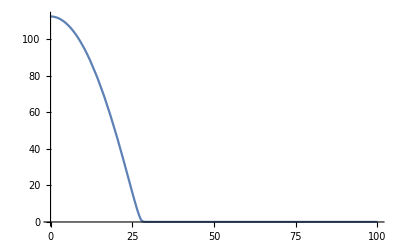

```mathematica
Plot[n[x,T/.params]/.initRun,{x,0,L/.params},PlotRange->All]
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[fTot,200];
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

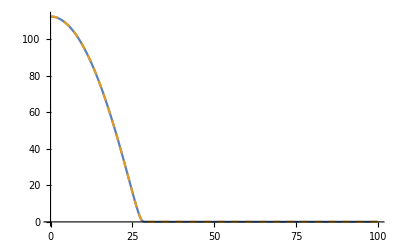

```mathematica
ListLinePlot[{
Transpose[{x,n[x,T]/.params/.initRun}/.x->(L*fdSetup["UnitGrid"]/.params)],
Transpose[{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

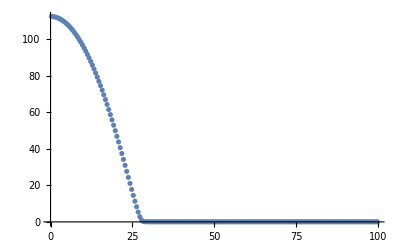

```mathematica
ListPlot[
Transpose[{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

```mathematica
rhoBar=Differences[Join[{0},MovingAverage[fdSetup["UnitGrid"],2],{1}]].(fdSetup["nVec"]/.statSol)
```

20.

## (D_v,ϵ)-sweep

The peaks of this system show a sharp knee. We use a non-uniform grid to resolve it well.

At large source strength ϵ  this model shows a transition towards mesa patterns.
Therefore, the mass-competition rate becomes very small in this regime (exponentially suppressed in the plateau length). 
To faithfully determine the eigenvalues in this regime, we use a very fine uniform grid.
To find the stationary state in such a large system, we build a custom Newton iterator that uses the special form of the Jacobian matrix in (u,v) variables (see setup).
Moreover, the Jacobian is compiled to speed up the calculation.

### Sweep for numerical LSA

```mathematica
DvEpsSweep1[L->100]=Monitor[
Block[{paramsL,
fdSetupNU,
iniSol,iniSolTemp,discSol,sol,solPrev,
jac,eval,evalS},
Table[
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
If[epsIter<10^-6,(*otherwise convergence to slow*)
iniSolTemp=Quiet[runTwoComponentSim[
fTot,
Join[{Dv->DvIter,eps->10^-6},fixedParams],
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
iniSol=runTwoComponentSim[
fTot,
paramsL,
{
(n[#,T/.paramsL]/.iniSolTemp)&,
(eta[#,T/.paramsL]/.iniSolTemp)&
},
T/.fixedParams
];,
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
];

discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
I
},
(*test for pattern having two peaks*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
{DvIter,epsIter},
 2I,
 2I
},
fdSetupNU=setupFiniteDifferenceEqs[fTot,(n[#*L,T]/L/.params/.iniSol)&,"dxMax"->1/300];

sol=Quiet[Check[FindRoot[
fdSetupNU["Eqs"]/.paramsL,
getInitGuess[fdSetupNU,paramsL,iniSol]
],3I,FindRoot::cvmit],FindRoot::cvmit];
If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I
},
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetupNU,
paramsL,
sol,
D[{eps Total[fTot[[2;;]]],-f+eps *(Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False
],MachinePrecision];
eval=Max[Re@Eigenvalues[jac]];
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetupNU,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
],MachinePrecision];
evalS=SortBy[SortBy[Eigenvalues[jac],Re[#]&][[-2;;]],Abs[Re@#]&][[-1]];
If[epsIter≥10^-3||epsIter≤10^-6,
{
{DvIter,epsIter},
eval,
evalS,
fdSetupNU,
sol
},
{
{DvIter,epsIter},
eval,
evalS
}]
]]],
{DvIter,10^Range[2/10,29/10,2/10]},{epsIter,10^Range[-6,-5/10,2/10]}
]],
N@{
Log10@epsIter,
Log10@DvIter,
ListPlot[Transpose@{fdSetupNU["UnitGrid"][[;;-2]],Differences@fdSetupNU["UnitGrid"]},PlotRange->All],
Plot[n[x*L,T]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetupNU["UnitGrid"],Re[fdSetupNU["nVec"]/.sol]},PlotRange->All]
}
];//AbsoluteTiming
```

```mathematica
fdSetupUV1000=setupFiniteDifferenceEqsUV[fTot,1000];
frJac=D[fdSetupUV1000["Eqs"],{fdSetupUV1000["Vars"]}];
ClearAll@compJac;
compJac=Block[{Part},Compile[{{x$,_Real,1},{p$,_Real,1}},Evaluate[frJac/.fixedParams/.Thread[{Dv,eps}->Table[p$[[ii]],{ii,1,2}]]/.Thread[fdSetupUV1000["Vars"]->Table[x$[[ii]],{ii,1,Length@fdSetupUV1000["Vars"]}]],RuntimeOptions->{"EvaluateSymbolically"->False}]]];//AbsoluteTiming
```

{200.758,Null}

```mathematica
compJacW[x_?(AllTrue[#,NumericQ]&),p_?(AllTrue[#,NumericQ]&)]:=SetPrecision[compJac[x,p],2000];
```

```mathematica
DvEpsSweep2[L->100]=Monitor[
Block[{paramsL,
iniSol,iniSolTemp,discSol,sol,
jac,eval,evalS,evec,evalIniCond,evalU},
Table[
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
If[epsIter<10^-6,(*otherwise convergence to slow*)
iniSolTemp=Quiet[runTwoComponentSim[
fTot,
Join[{Dv->DvIter,eps->10^-6},fixedParams],
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
iniSol=runTwoComponentSim[
fTot,
paramsL,
{
(n[#,T/.paramsL]/.iniSolTemp)&,
(eta[#,T/.paramsL]/.iniSolTemp)&
},
T/.fixedParams
];,
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
];

discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
I
},
(*test for pattern having two peaks, first condition tests whether the mesa separated from the boundary x=0 (splitting of upper plateau),
second condition tests for splitting of lower plateau*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
{DvIter,epsIter},
 2I,
 2I
},
sol=Quiet[Check[newton[
fdSetupUV1000,
getInitGuessUV[fdSetupUV1000,paramsL,iniSol][[All,2]],
compJacW,
paramsL,"DampingFactor"->1,"TextOutput"->False,"TimingOutput"->False],3I,{newton::notConverging,newton::divZero}],{newton::notConverging,newton::divZero}];

If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I
},
evalIniCond=Riffle[
Differences[Join[{fdSetupUV1000["uVec"][[1]]},fdSetupUV1000["uVec"],{fdSetupUV1000["uVec"][[-1]]}],1,2],
Differences[Join[{fdSetupUV1000["vVec"][[1]]},fdSetupUV1000["vVec"],{fdSetupUV1000["vVec"][[-1]]}],1,2]
]/.sol;

jac=SetPrecision[Normal@constructGluedJacobianUV[
fdSetupUV1000,
paramsL,
sol,
D[{f/(1-Du/Dv)+eps fTot[[2]],-f/(1-Du/Dv)+eps fTot[[3]]}/.{n->(u+v),η->(v+Du/Dv u)},{{u,v}}],(*reaction + source terms of u and v*)
"Reverse"->False
],MachinePrecision];
eval=Max@Eigenvalues[jac,-5,Method->{"Arnoldi","Tolerance"->10^-20,"StartingVector"->evalIniCond}];
jac=SetPrecision[Normal@constructGluedJacobianUV[
fdSetupUV1000,
paramsL,
sol,
D[{f/(1-Du/Dv)+eps fTot[[2]],-f/(1-Du/Dv)+eps fTot[[3]]}/.{n->(u+v),η->(v+Du/Dv u)},{{u,v}}],(*reaction + source terms of u and v*)
"Reverse"->False,
"Symmetric"->True
],MachinePrecision];
evalS=Max@Eigenvalues[jac,-5,Method->{"Arnoldi","Tolerance"->10^-20,"StartingVector"->evalIniCond}];
If[epsIter≥10^-3||epsIter≤10^-6,
{
{DvIter,epsIter},
eval,
evalS,
fdSetupUV1000,
sol
},
{
{DvIter,epsIter},
eval,
evalS
}]
]]],
{DvIter,10^Range[26/10,7,2/10]},{epsIter,10^Range[-6,-5/10,2/10]}
]],
N@{If[NumericQ[eval],eval],
Log10@epsIter,
Log10@DvIter,
Plot[n[x*L,T]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetupUV1000["UnitGrid"],Re[fdSetupUV1000["uVec"]/.sol]},PlotRange->All]
}
];//AbsoluteTiming
```

{255.697,Null}

```mathematica
DvEpsSweep[L->100]=Join[DvEpsSweep1[L->100],DvEpsSweep2[L->100]];
```

### Threshold approximations

#### Approximations for the growth rate

Note: the stationary state for the constant reaction rate model is independent of D_v.

```mathematica
fdSetupMC=setupFiniteDifferenceEqsMC[f,2000];
```

```mathematica
analytThresholds=analytics[fTot,Join[{eps->10^-5},fixedParams],fdSetupMC,"DvAnalytic"->True];
```

Assume Dv-independent stationary state.

#### Improved approximation of the stability threshold by shifting all source terms into v and explicitly accounting for the nullcline deformation induced by the u sources

```mathematica
fdSetupMod=setupFiniteDifferenceEqsMod[fTot,2000];
frJac=D[fdSetupMod["Eqs"],{fdSetupMod["Vars"]}];
ClearAll@compJacMod;
compJacMod=Block[{Part},Compile[{{x$,_Real,1},{p$,_Real,1}},Evaluate[frJac/.DeleteCases[fixedParams,L->_]/.Thread[{eps,rhobar,L}->Table[p$[[ii]],{ii,1,3}]]/.Thread[fdSetupMod["Vars"]->Table[x$[[ii]],{ii,1,Length@fdSetupMod["Vars"]}]],RuntimeOptions->{"EvaluateSymbolically"->False}]]];//AbsoluteTiming
```

{189.617,Null}

```mathematica
compJacModW[x_?(AllTrue[#,NumericQ]&),p_?(AllTrue[#,NumericQ]&)]:=SetPrecision[compJacMod[x,p],1000];
```

```mathematica
Monitor[analyticsImproved=analyticsMod[fTot,10^Range[-6,-1,1/10],fixedParams,fdSetupMod,compJacModW];,
{N@Log10@eps,Plot[n[x,50000]/.initRun,{x,0,L/.fixedParams}]}]//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {«1022»,50000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{882.342,Null}

```mathematica
Monitor[epsStop=Table[Block[{ee},
ee=eps/.FindRoot[analyticsImproved[["sigmaED"]]/.Dv->dd,{eps,analytThresholds["epsStop"]/.Dv->dd}];
{dd,Re@ee}]
,{dd,10^Range[0,7,0.1]}],dd];
```

InterpolatingFunction::dmval: Input value {8.94187×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Stability regions

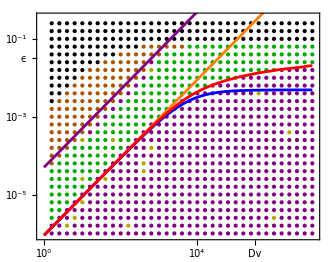

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve peak splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweep[L->100],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],

AbsoluteThickness[2],
(*epsStop diff. limited*)
Orange,
Line[Select[(({Log10[Dv],Log10[-#["sigmaD"]/#["<sRhoRho>"]]}&@analytThresholds)/.Dv->10^#)&/@Range[0,7,0.1],Im[#[[2]]]==0&]],
(*full epsStop*)
Blue,
Line[Select[(({Log10[Dv],Log10[#["epsStop"]]}&@analytThresholds)/.Dv->10^#)&/@Range[0,7,0.1],Im[#[[2]]]==0&]],
(*improved approximation shifting source terms into the v species*)
Red,
Line[Select[Log10@epsStop,NumericQ[#[[2]]]&]],
(*mesa splitting, Eq. (H9)*)
Purple,
Line[{
{0,Log10[10*Dv/(p*L^2)]/.Dv->1},
{8,Log10[10*Dv/(p*L^2)]/.Dv->10^8}
}/.params]
},
PlotRange->{{-0.05,7.05},{-6.05,-0.45}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-1.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{6,"10^6",{0,0.02}},{5.5,"Dv",{0,0}}},
None
}
}
]
```

### Profiles

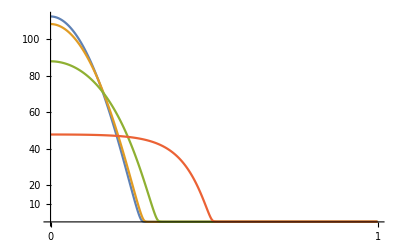

```mathematica
ListLinePlot[Transpose[{#[[-2]]["UnitGrid"],#[[-2]]["uVec"]+#[[-2]]["vVec"]/.#[[-1]]}]&/@DvEpsSweep[L->100][[-5,{1,-13,-9,-6}]],
PlotRange->All,
Ticks->{{0,1},{10,20,40,60,80,100}}]
```

### Rates

The numerical values depicted at Dv =10^8 are obtained in the cAC limit! As we see that the rate is already nicely saturated to its reaction-limited value, we can compare to the analytics at Dv=10^8.

#### σ(D_v) at ϵ=10^-3

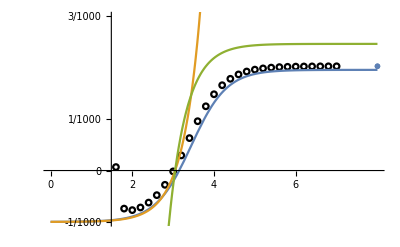

```mathematica
logEps=3;
ind=First@First@Position[N[DvEpsSweep[L->100][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->100][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListPlot[{{8,DvEpsSweepRL[L->100][[ind,2]]}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thickness[0.2]}],FaceForm[None],Rotate[Rectangle[],45Degree]}],0.04}],
Plot[Evaluate[{analytThresholds["sigma"],
(#["sigmaD"]-eps Abs@#["<sRhoRho>"])&@analytThresholds,
(1-eps Abs@#["<sRhoRho>"]/#["sigmaD"])/(1/#["sigmaR"])&@analytThresholds}/.eps->10^-logEps/.Dv->10^logDv],{logDv,0,8}],
PlotRange->{-10^-3,3*10^-3},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit"
},
Ticks->{{0,2,4,6},{-10^-3,0,10^-3,3*10^-3}}
]
```

#### σ(D_v) at ϵ=10^-5

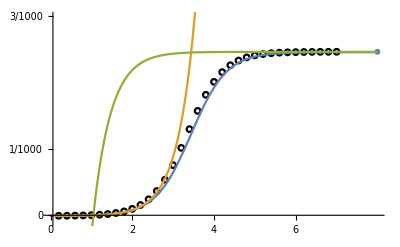

```mathematica
logEps=5;
ind=First@First@Position[N[DvEpsSweep[L->100][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweep[L->100][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
ListPlot[{{8,DvEpsSweepRL[L->100][[ind,2]]}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thickness[0.2]}],FaceForm[None],Rotate[Rectangle[],45Degree]}],0.04}],
Plot[Evaluate[{analytThresholds["sigma"],
(#["sigmaD"]-eps Abs@#["<sRhoRho>"])&@analytThresholds,
(1-eps Abs@#["<sRhoRho>"]/#["sigmaD"])/(1/#["sigmaR"])&@analytThresholds}/.eps->10^-logEps/.Dv->10^logDv],{logDv,0,8}],
PlotRange->{-10^-4,3*10^-3},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit"
},
Ticks->{{0,2,4,6},{-6*10^-3,-3*10^-3,0,10^-3,3*10^-3}}
]
```

## cAC limit

#### Loop for sweeping

We use again a uniform grid.

```mathematica
fdSetupRL=setupFiniteDifferenceEqsRL[fTot,1000];
```

```mathematica
DvEpsSweepRL[L->100]=Monitor[
Block[{paramsL,
fdSetupC,
iniSol,discSol,sol,
jac,eval},
Table[
paramsL=Join[{Dv->10^6,eps->epsIter},fixedParams];
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<1,
PrintTemporary["No pattern!"];
{
epsIter,
 I
},
(*test for pattern having split*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
epsIter,
 2I
},
sol=Quiet[Check[FindRoot[
fdSetupRL["Eqs"]/.paramsL,
getInitGuessRL[fdSetupRL,paramsL,iniSol],AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->100,MaxIterations->20],3I,{FindRoot::cvmit,FindRoot::lstol}],{FindRoot::cvmit,FindRoot::lstol}];
If[sol===3I,
PrintTemporary["Not converging!"];
{
epsIter,
3I
},
jac=SetPrecision[Normal@constructGluedJacobianRL[
fdSetupRL,
paramsL,
sol,
D[fTot[[1]]+eps *fTot[[2]],n],
"Reverse"->False
],100];
eval=First@Re@Eigenvalues[jac,-1,Method->{"Arnoldi",Tolerance->10^-20}];
{
epsIter,
eval,
sol
}]
]
],{epsIter,10^Range[-6,-5/10,2/10]}
]],
N@{
epsIter,
Plot[n[x*L,T/100]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetupRL["UnitGrid"],Re[fdSetupRL["nVec"]/.sol]},PlotRange->All]
}
];//AbsoluteTiming
```

{595.431,Null}

#### Plot

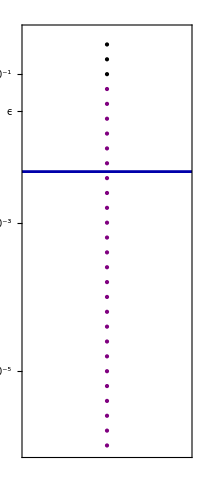

```mathematica
Graphics[{
(*mass-competition instability*)
Purple,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Re[#[[2]]]<0&][[All,1]]],
(*NDSolve peak splitting*)
Darker@Orange,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[{1,#}&/@Log10@Select[DvEpsSweepRL[L->100],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],

AbsoluteThickness[2],
(*full epsStop*)
Darker@Blue,
Line[{{0,#},{2,#}}&@((Log10[#["epsStop"]]&@analytThresholds)/.Dv->10^10)]
},
PlotRange->{{0.45,1.55},{-6.05,-0.45}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-1.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
None,
None
}
}
]
```

### Growth rates in shadow limit

InterpolatingFunction::dmval: Input value {1.×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.25893×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

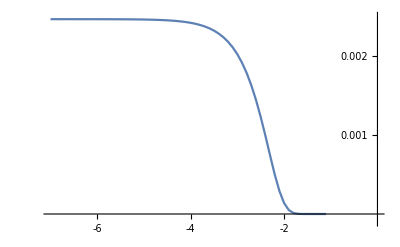

```mathematica
ListPlot[{Log10@#,analyticsImproved[["sigmaR"]]/.eps->#}&/@(10^Range[-7,-1.1,0.1]),Joined->True,PlotRange->{-10^-4,2.5*10^-3},
Ticks->{{-6,-4,-2},{0.001,0.002}}]
```

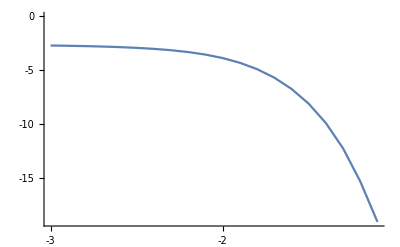

```mathematica
ListPlot[{Log10@#,Log10@analyticsImproved[["sigmaR"]]/.eps->#}&/@(10^Range[-3,-1.1,0.1]),Joined->True,
Ticks->{{-3,-2,-1},{-20,-15,-10,-5,0}}]
```

## Source terms (s_1,s_2)=(p-n,0)

### Model setup

Const-reaction-rate reaction kinetics in (n,η) variables

```mathematica
f=(η-10n/(1+n^2));(*\tilde{f}*)
source=(p-n);
fTot={f,0,source};
```

```mathematica
fixedParams={p->20,Du->1,L->100,T->10^8};
params=Join[{eps->10^-5,Dv->10^3},fixedParams];
```

## Stationary pattern

```mathematica
initRun=runTwoComponentSim[
fTot,
params,
{
100Sech[#/5]^2&,
0&
},
T/.fixedParams
];
```

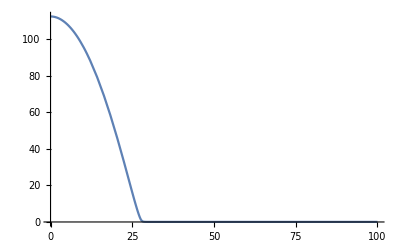

```mathematica
Plot[n[x,T/.params]/.initRun,{x,0,L/.params},PlotRange->All]
```

```mathematica
fdSetup=setupFiniteDifferenceEqs[fTot,200];
```

```mathematica
statSol=Block[{n,eta},FindRoot[
fdSetup["Eqs"]/.params,
getInitGuess[fdSetup,params,initRun]
]
];
```

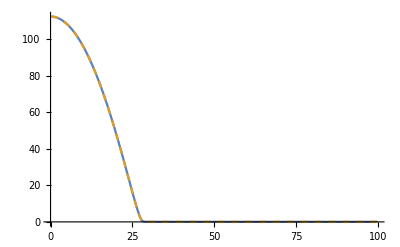

```mathematica
ListLinePlot[{
Transpose[{x,n[x,T]/.params/.initRun}/.x->(L*fdSetup["UnitGrid"]/.params)],
Transpose[{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}]
},
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

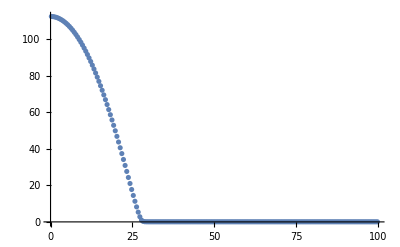

```mathematica
ListPlot[
Transpose[{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
PlotRange->All,
PlotStyle->{Default,Dashed}
]
```

```mathematica
rhoBar=Differences[Join[{0},MovingAverage[fdSetup["UnitGrid"],2],{1}]].(fdSetup["nVec"]/.statSol)
```

20.

## (D_v,ϵ)-sweep

The peaks of this system show a sharp knee. We use a non-uniform grid for the finite-differences discretization to resolve it well.

### Sweep for numerical LSA

```mathematica
DvEpsSweepV[L->100]=Monitor[
Block[{paramsL,
fdSetupNU,
iniSol,iniSolTemp,discSol,sol,solPrev,
jac,eval,evalS},
Table[
paramsL=Join[{Dv->DvIter,eps->epsIter},fixedParams];
If[epsIter<10^-6,(*otherwise convergence to slow*)
iniSolTemp=Quiet[runTwoComponentSim[
fTot,
Join[{Dv->DvIter,eps->10^-6},fixedParams],
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
iniSol=runTwoComponentSim[
fTot,
paramsL,
{
(n[#,T/.paramsL]/.iniSolTemp)&,
(eta[#,T/.paramsL]/.iniSolTemp)&
},
T/.fixedParams
];,
iniSol=Quiet[runTwoComponentSim[
fTot,
paramsL,
{
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["nVec"]/.statSol}],
Interpolation[Transpose@{fdSetup["UnitGrid"]*L/.params,fdSetup["etaVec"]/.statSol}]
},
T/.fixedParams
],InterpolatingFunction::dmval];
];

discSol=n[x*L,T]/.paramsL/.iniSol/.x->Range[0.02,1,0.04];
(*test for pattern being uniform*)
If[Variance[discSol]<10^-2,
PrintTemporary["No pattern!"];
{
{DvIter,epsIter},
 I,
I
},
(*test for pattern having two peaks*)
If[(discSol[[1]]<Max[discSol]/2 ||Length@Select[FindPeaks[discSol],#[[2]]>Max[discSol]/2&]>1),
PrintTemporary["Peak splitted!"];
{
{DvIter,epsIter},
 2I,
 2I
},
fdSetupNU=setupFiniteDifferenceEqs[fTot,(n[#*L,T]/L/.params/.iniSol)&,"dxMax"->1/300];

sol=Quiet[Check[FindRoot[
fdSetupNU["Eqs"]/.paramsL,
getInitGuess[fdSetupNU,paramsL,iniSol]
],3I,FindRoot::cvmit],FindRoot::cvmit];
If[sol===3I,
PrintTemporary["Not converging!"];
{
{DvIter,epsIter},
3I,
3I
},
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetupNU,
paramsL,
sol,
D[{eps Total[fTot[[2;;]]],-f+eps *(Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False
],MachinePrecision];
eval=Max[Re@Eigenvalues[jac]];
jac=SetPrecision[Normal@constructGluedJacobian[
fdSetupNU,
paramsL,
sol,
D[{eps (fTot[[2]]+fTot[[3]]),-fTot[[1]]+eps (Du/Dv*fTot[[2]]+fTot[[3]])},{{n,η}}],
"Reverse"->False,
"Symmetric"->True
],MachinePrecision];
evalS=SortBy[SortBy[Eigenvalues[jac],Re[#]&][[-2;;]],Abs[Re@#]&][[-1]];
If[epsIter≥10^-3||epsIter≤10^-6,
{
{DvIter,epsIter},
eval,
evalS,
fdSetupNU,
sol
},
{
{DvIter,epsIter},
eval,
evalS
}]
]]],
{DvIter,10^Range[2/10,7,2/10]},{epsIter,10^Range[-6,-5/10,2/10]}
]],
N@{
Log10@epsIter,
Log10@DvIter,
ListPlot[Transpose@{fdSetupNU["UnitGrid"][[;;-2]],Differences@fdSetupNU["UnitGrid"]},PlotRange->All],
Plot[n[x*L,T]/.paramsL/.iniSol,{x,0,1}],
ListPlot[Transpose@{fdSetupNU["UnitGrid"],Re[fdSetupNU["nVec"]/.sol]},PlotRange->All]
}
];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{1572.96,Null}

### Threshold approximations

Note: the stationary state for the constant reaction rate model is independent of D_v.

```mathematica
fdSetupMC=setupFiniteDifferenceEqsMC[f,2000];
```

```mathematica
analytThresholds=analytics[fTot,Join[{eps->10^-5},fixedParams],fdSetupMC,"DvAnalytic"->True];
```

Assume Dv-independent stationary state.

### Stability regions

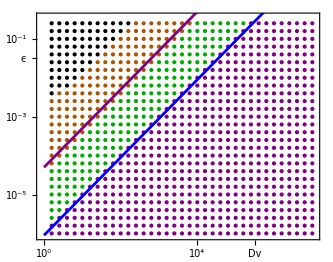

```mathematica
Graphics[{
(*single-domain instability, non-oscillatory*)
Darker@Red,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]==0&&Re[#[[3]]]>0&][[All,1]]],
(*single-domain instability, oscillatory*)
Darker@Blue,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Re[#[[2]]]<Re[#[[3]]]&&Im[#[[3]]]≠0&&Re[#[[3]]]>0&][[All,1]]],
(*mass-competition instability*)
Purple,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]==0&&Re[#[[2]]]>0&][[All,1]]],
(*two-domain instability, oscillatory*)
Pink,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Re[#[[2]]]>Re[#[[3]]]&&Im[#[[2]]]≠0&&Re[#[[2]]]>0&][[All,1]]],
(*stable*)
Darker@Green,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Re[#[[3]]]<0&&Re[#[[2]]]<0&][[All,1]]],
(*NDSolve peak splitting*)
Darker@Orange,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Im[#[[2]]]==2&&Re[#[[2]]]==0&][[All,1]]],
(*FindRoot not converging*)
Darker@Yellow,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Im[#[[2]]]==3&&Re[#[[2]]]==0&][[All,1]]],
(*NDSolve uniform*)
Black,
Point[Log10@Select[Flatten[DvEpsSweepV[L->100],1],Im[#[[2]]]==1&&Re[#[[2]]]==0&][[All,1]]],

AbsoluteThickness[2],
(*full epsStop*)
Blue,
Line[Select[(({Log10[Dv],Log10[#["epsStop"]]}&@analytThresholds)/.Dv->10^#)&/@Range[0,7,0.1],Im[#[[2]]]==0&]],
(*mesa splitting, Eq. (H9)*)
Purple,
Line[{
{0,Log10[10*Dv/(p*L^2)]/.Dv->1},
{8,Log10[10*Dv/(p*L^2)]/.Dv->10^8}
}/.params]
},
PlotRange->{{-0.05,7.05},{-6.05,-0.45}},PlotRangeClipping->True,
Frame->True,
BaseStyle->14,FrameStyle->Black,
FrameTicks->{{
{{-7,"10^-7",{0,0.02}},{-5,"10^-5",{0,0.02}},{-3,"10^-3",{0,0.02}},{-1.5,"ϵ  ",{0,0}},{-1,"10^-1",{0,0.02}}},
None
},{
{{0,"10^0",{0,0.02}},{2,"10^2",{0,0.02}},{4,"10^4",{0,0.02}},{6,"10^6",{0,0.02}},{5.5,"Dv",{0,0}}},
None
}
}
]
```

### Rates

#### σ(D_v) at ϵ=10^-1

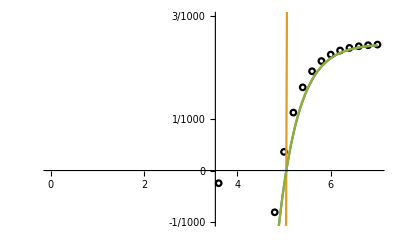

```mathematica
logEps=1;
ind=First@First@Position[N[DvEpsSweepV[L->100][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->100][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[Evaluate[{analytThresholds["sigma"],
(#["sigmaD"]-eps Abs@#["<sRhoRho>"])&@analytThresholds,
(1-eps Abs@#["<sRhoRho>"]/#["sigmaD"])/(1/#["sigmaR"])&@analytThresholds}/.eps->10^-logEps/.Dv->10^logDv],{logDv,0,7}],
PlotRange->{-10^-3,3*10^-3},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit"
},
Ticks->{{0,2,4,6},{-10^-3,0,10^-3,3*10^-3}}
]
```

#### σ(D_v) at ϵ=10^-3

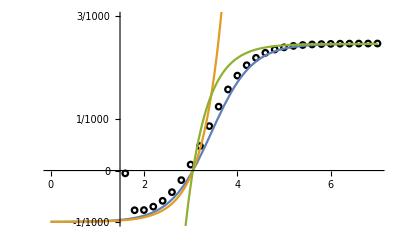

```mathematica
logEps=3;
ind=First@First@Position[N[DvEpsSweepV[L->100][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->100][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[Evaluate[{analytThresholds["sigma"],
(#["sigmaD"]-eps Abs@#["<sRhoRho>"])&@analytThresholds,
(1-eps Abs@#["<sRhoRho>"]/#["sigmaD"])/(1/#["sigmaR"])&@analytThresholds}/.eps->10^-logEps/.Dv->10^logDv],{logDv,0,7}],
PlotRange->{-10^-3,3*10^-3},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit"
},
Ticks->{{0,2,4,6},{-10^-3,0,10^-3,3*10^-3}}
]
```

#### σ(D_v) at ϵ=10^-5

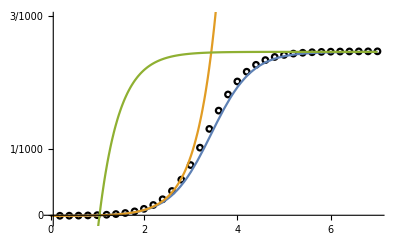

```mathematica
logEps=5;
ind=First@First@Position[N[DvEpsSweepV[L->100][[1,All,1,2]]],x_/;Abs[x-10^-logEps]<10^-7];
Show[
ListPlot[
{{Log10@#[[1,1]],#[[2]]}&/@DvEpsSweepV[L->100][[All,ind]]},
PlotRange->All,PlotMarkers->{Graphics[{Black,Circle[]}],0.04}
],
Plot[Evaluate[{analytThresholds["sigma"],
(#["sigmaD"]-eps Abs@#["<sRhoRho>"])&@analytThresholds,
(1-eps Abs@#["<sRhoRho>"]/#["sigmaD"])/(1/#["sigmaR"])&@analytThresholds}/.eps->10^-logEps/.Dv->10^logDv],{logDv,0,7}],
PlotRange->{-10^-4,3*10^-3},
PlotLegends->{
"finite differences eigenvalues",
"σ",
"σ_McKay",
"σ_diffLimit"
},
Ticks->{{0,2,4,6},{-6*10^-3,-3*10^-3,0,10^-3,3*10^-3}}
]
```